```mathematica
bead100image=-Graphics-;
```

```mathematica
imgdata=Flatten[Table[{i,j,ImageData[bead100image][[i,j]]},{i,Length[ImageData[bead100image]]},{j,Length[ImageData[bead100image][[i]]]}],1];
```

```mathematica
gaussianmodel=a Exp[-b ((x-x00)^2+(y-y00)^2)]+c;
```

```mathematica
fit=FindFit[imgdata,gaussianmodel,{a,b,{c,0},{x00,ImageDimensions[bead100image][[1]]/2},{y00,ImageDimensions[bead100image][[2]]/2}},{x,y}]
```

{a→0.00594537,b→0.117141,c→0.00387444,x00→32.6225,y00→30.7759}

```mathematica
test2=-Graphics-;
```

```mathematica
imgdata2=Flatten[Table[{i,j,ImageData[test2][[i,j]]},{i,Length[ImageData[test2]]},{j,Length[ImageData[test2][[i]]]}],1];
```

```mathematica
fit2=FindFit[imgdata2,{gaussianmodel,{a+c>ImageMeasurements[test2,"Max"]}},{a,b,{c,0},{x0,ImageDimensions[test2][[1]]/2},{y0,ImageDimensions[test2][[2]]/2}},{x,y}]
```

FindFit::nrnum: The function value 1/2 ((-0.00314336+1. ⅇ^(-1. Plus[«2»]))^2+«9»+«4086») is not a real number at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindFit::nrgnum: The gradient is not a vector of real numbers at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

FindFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[«1»],Block},{0,{{{},1,0,Hold[a],0,0},{{},1,1,Hold[b],0,0},{{},1,2,Hold[c],0,0},{{},1,3,Hold[x0],0,0},{{},1,4,Hold[y0],0,0}}},{«1»},«1»,{«1»},{None,None,None}] failed at {1.,1.,0.,32.,32.}.

FindFit[{{1,1,0.00314336},{1,2,0.00325017},4092,{64,63,0.0030518},{64,64,0.00311284}},{c+1,1},1,{x,y}]
 |  |  |  |

```mathematica
Show[Plot3D[gaussianmodel/. fit2,{x,ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{y,ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},PlotRange->All,PlotPoints->100,MaxRecursion->5],ListPointPlot3D[imgdata2,PlotStyle->Directive[PointSize[Medium],Red]],PlotRange->{{ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},All}]
```

General::ivar: 16.0003 is not a valid variable.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.0003 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1.,1.,0.00314336},{1.,2.,0.00325017},{1.,3.,0.00300603},«5»,{1.,9.,0.00318914},{1.,10.,0.00309758},«4086»},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.3236 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{1,1,0.00314336},{1,2,0.00325017},{1,3,0.00300603},«5»,{1,9,0.00318914},{1,10,0.00309758},«4086»},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
0.25/0.046
```

5.43478

```mathematica
5.434782608695652^2
```

29.5369

```mathematica
dum2pixel[dum_]:=(dum/2)/0.046
```

```mathematica
dum2pixel[0.5]
```

5.43478

```mathematica
disc500=Piecewise[{{1,x^2+y^2<29.53686200378072}},0]
```

Piecewise[{{1, x^2+y^2<29.5369}, {0, True}}]

```mathematica
disc200=Piecewise[{{1,x^2+y^2<dum2pixel[0.2]^2}},0]
```

Piecewise[{{1, x^2+y^2<4.7259}, {0, True}}]

```mathematica
discgenerator[d_]:=Piecewise[{{1,x^2+y^2<dum2pixel[d]^2}},0]
```

```mathematica
discgeneratorfunc[d_,x0_,y0_]:=discgenerator[d]/. {x->x0,y->y0}
```

```mathematica
convolintensityfunc[d_]:=Table[NIntegrate[discgeneratorfunc[d,x,y]*(ⅇ^(-b ((x0-x)^2+(y0-y)^2))/.fit),{x,-Infinity,Infinity},{y,-Infinity,Infinity}],{x0,-50,50},{y0,-50,50}]
```

```mathematica
cov200=convolintensityfunc[0.2];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

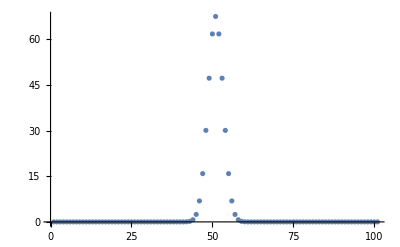

```mathematica
ListPlot[Total[convolintensityfunc[0.2]],PlotRange->All]
```

```mathematica
real=Total[ImageData[-Graphics-]]
```

{22329.,22401.1,22099.,22095.,22759.,22549.,22335.,22429.,22794.,22432.,22547.,22728.,22877.,22950.,22844.9,23504.9,23901.1,24698.,26471.,30867.,38217.,53043.,73689.,98228.,110693.,105898.,86580.,63795.,45644.9,34738.,28041.,25349.1,24400.9,23213.,22933.,22904.,22945.,22718.,22485.,22249.1,22743.,22665.,22339.,22584.,22153.,22448.,22494.,22064.,22448.6}

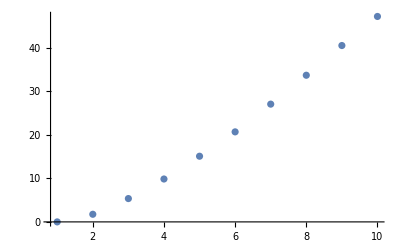

```mathematica
ListPlot[(%400-%400[[1]])/Max[%400]*70,PlotRange->All]
```

```mathematica
ImageAdjust/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

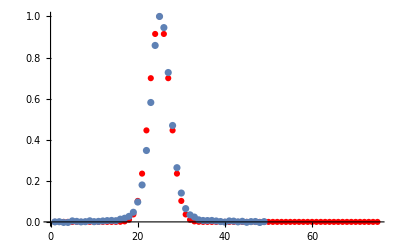

```mathematica
Show[ListPlot[Drop[Total[cov200]/Max[Total[cov200]],26],PlotRange->All,PlotStyle->Red],ListPlot[(real-real[[1]])/Max[real-real[[1]]],PlotRange->All]]
```

```mathematica
convolintensity
```

convolintensity

```mathematica
Total[convolintensity]
```

Total[convolintensity]

```mathematica
Interpolation[Total[convolintensity]]
```

Interpolation::innd: First argument in Total[convolintensity] does not contain a list of data and coordinates.

Interpolation[Total[convolintensity]]

```mathematica
Plot[%424[x],{x,1.,101.},PlotRange->All]
```

FindFit::nrnum: The function value 1/2 ((-0.00314336+1. 2.71828^(-1. Plus[«2»]))^2+«9»+«4086») is not a real number at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindFit::nrgnum: The gradient is not a vector of real numbers at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

FindFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[«1»],Block},{0,{{{},1,0,Hold[a],0,0},{{},1,1,Hold[b],0,0},{{},1,2,Hold[c],0,0},{{},1,3,Hold[x0],0,0},{{},1,4,Hold[y0],0,0}}},{«1»},«1»,{«1»},{None,None,None}] failed at {1.,1.,0.,32.,32.}.

FindFit::nrnum: The function value 1/2 ((-0.00314336+1. ⅇ^(-1. Plus[«2»]))^2+«9»+«4086») is not a real number at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindFit::nrgnum: The gradient is not a vector of real numbers at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

General::stop: Further output of FindFit::nrgnum will be suppressed during this calculation.

FindFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[«1»],Block},{0,{{{},1,0,Hold[a],0,0},{{},1,1,Hold[b],0,0},{{},1,2,Hold[c],0,0},{{},1,3,Hold[x0],0,0},{{},1,4,Hold[y0],0,0}}},{«1»},«1»,{«1»},{None,None,None}] failed at {1.,1.,0.,32.,32.}.

FindFit::nrnum: The function value 1/2 ((-0.00314336+1. 2.71828^(-1. Plus[«2»]))^2+«9»+«4086») is not a real number at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

General::stop: Further output of FindFit::nrnum will be suppressed during this calculation.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.

FindFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[«1»],Block},{0,{{{},1,0,Hold[a],0,0},{{},1,1,Hold[b],0,0},{{},1,2,Hold[c],0,0},{{},1,3,Hold[x0],0,0},{{},1,4,Hold[y0],0,0}}},{«1»},«1»,{«1»},{None,None,None}] failed at {1.,1.,0.,32.,32.}.

General::stop: Further output of FindFit::grad will be suppressed during this calculation.

-Graphics-

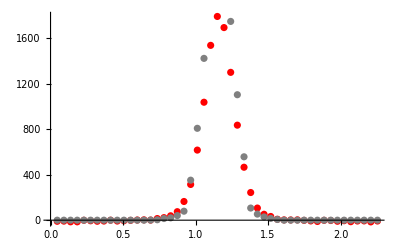
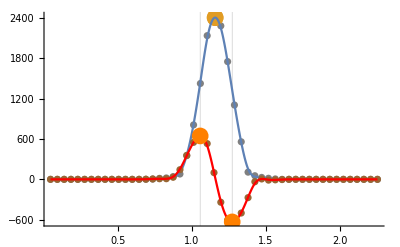
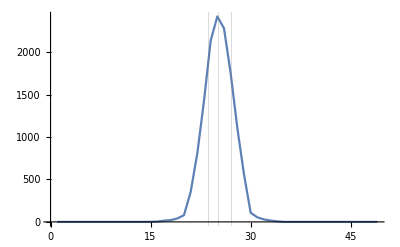
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allplots[-Graphics-,5]
```

```mathematica
allinfo[-Graphics-,5]
```

{True,T,267.895,465.382,2403.51,0.252772,0.736,False,NA,NA,0.046 NA,0.388088,0.0181174,0.0160151,-0.0146364,-0.0188182,0.836273,0.916667,0.401775,-2.07662,0.0992338,0.900766,0.552899,L}

```mathematica
allinfo[-Graphics-,5]
```

{True,T,568.136,634.063,20133.5,0.382021,1.058,False,NA,NA,0.046 NA,0.526644,0.0224004,0.023763,-0.0125455,0.,0.939817,0.984733,0.825769,-2.93741,0.0652228,0.934777,0.527539,L}

```mathematica
Total[convolintensity]
```

Total[convolintensity]

```mathematica
MatrixPlot[convolintensity]
```

MatrixPlot::mat0: Argument convolintensity at position 1 is not a matrix.

MatrixPlot[convolintensity]

```mathematica
ImageData[Image[convolintensity]]
```

Image::imgarray: The specified argument convolintensity should be an array of rank 2 or 3 with machine-sized numbers.

ImageData::imginv: Expecting an image or graphics instead of Image[convolintensity].

ImageData[Image[convolintensity]]

```mathematica
allinfo[ImageAdjust[Image[convolintensity]],5]
```

Image::imgarray: The specified argument convolintensity should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of Image[convolintensity].

ImageData::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

ImageData::argt: ImageData called with 0 arguments; 1 or 2 arguments are expected.

If[ImageData[]=={},If[intensitycheck[ImageAdjust[Image[convolintensity]],5]<intensitythreshold||backgroundbadcheck[ImageAdjust[Image[convolintensity]],5]||!backgrounddeletecomponentcheck[ImageAdjust[Image[convolintensity]],5]||Total[cleanYmean[ImageAdjust[Image[convolintensity]],5]]≤0,{boundarycheck[ImageAdjust[Image[convolintensity]],5],F or bad background,intensitycheck[ImageAdjust[Image[convolintensity]],5],Mean[backgroundintensities[ImageAdjust[Image[convolintensity]],5]],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},If[findintensitypeaks[ImageAdjust[Image[convolintensity]],5]=={},{boundarycheck[ImageAdjust[Image[convolintensity]],5],T,intensitycheck[ImageAdjust[Image[convolintensity]],5],meanbackground[ImageAdjust[Image[convolintensity]],5],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},Module[{intensitycheckresult$,signalstrength$,averagebackground$,meanYmainpeakintensityoverbackground$,widthX$,halfAreaWidth$,meanwidth$,secondpeakornot$,intensitysecondpeak$,secondpeakdirection$,peaksdistance$,tailornot$,directiontail$,lengthtail$,discR$,intensitycentroidtodisccenterx$,peaktodiscX$,brightesttodisccenterX$,brightesttodisccenterY$,diskcoverage$,polygoncoverage$,areaofKT$,tiltangle$,elongationratio$,semiaxesratio$,boundboxX$,leftrightratio$,skewdirec$},intensitycheckresult$=T;signalstrength$=intensitycheck[ImageAdjust[Image[convolintensity]],5];averagebackground$=meanbackground[ImageAdjust[Image[convolintensity]],5];meanYmainpeakintensityoverbackground$=mainpeak[ImageAdjust[Image[convolintensity]],5]⟦2⟧;meanwidth$=meanareawidth[ImageAdjust[Image[convolintensity]],5] pixelsize;boundboxX$=boundingboxX[ImageAdjust[Image[convolintensity]],5] pixelsize;secondpeakornot$=ifreallysecondpeak[ImageAdjust[Image[convolintensity]],5];intensitysecondpeak$=secondpeakintensity[ImageAdjust[Image[convolintensity]],5];secondpeakdirection$=directionsecondpeak[ImageAdjust[Image[convolintensity]],5];peaksdistance$=distancetwopeaks[ImageAdjust[Image[convolintensity]],5] pixelsize;discR$=boundingdiscRadius[ImageAdjust[Image[convolintensity]],5] pixelsize;brightesttodisccenterX$=brightesttodisccenter[ImageAdjust[Image[convolintensity]],5]⟦1⟧ pixelsize;brightesttodisccenterY$=brightesttodisccenter[ImageAdjust[Image[convolintensity]],5]⟦2⟧ pixelsize;diskcoverage$=boundingdiskcoverage[ImageAdjust[Image[convolintensity]],5];polygoncoverage$=convexcoverage[ImageAdjust[Image[convolintensity]],5];areaofKT$=areacomponentofinterest[ImageAdjust[Image[convolintensity]],5] pixelsize pixelsize;tiltangle$=angle[ImageAdjust[Image[convolintensity]],5];elongationratio$=elongation[ImageAdjust[Image[convolintensity]],5];semiaxesratio$=semiaxesRatio[ImageAdjust[Image[convolintensity]],5];leftrightratio$=leftrightarearatio[ImageAdjust[Image[convolintensity]],5];skewdirec$=skewdirection[ImageAdjust[Image[convolintensity]],5];intensitycentroidtodisccenterx$=N[intensitycentroidTodisccenterX[ImageAdjust[Image[convolintensity]],5] pixelsize];peaktodiscX$=peakTodisccenterX[ImageAdjust[Image[convolintensity]],5] pixelsize;{boundarycheck[ImageAdjust[Image[convolintensity]],5],intensitycheckresult$,signalstrength$,averagebackground$,meanYmainpeakintensityoverbackground$,meanwidth$,boundboxX$,secondpeakornot$,intensitysecondpeak$,secondpeakdirection$,peaksdistance$,discR$,intensitycentroidtodisccenterx$,peaktodiscX$,brightesttodisccenterX$,brightesttodisccenterY$,diskcoverage$,polygoncoverage$,areaofKT$,tiltangle$,elongationratio$,semiaxesratio$,leftrightratio$,skewdirec$}]]],{boundarycheck[ImageAdjust[Image[convolintensity]],5],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}]

```mathematica
convtable=Table[convolintensityfunc[d/10],{d,1,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Table[{{"d=",d/10},allinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,2,10}]
```

{{{d=,1/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,3/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,2/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,1/2},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,3/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,7/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,4/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,9/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,1},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}}}

```mathematica
simutable={{{"d=",1/5},{0.000028573631401648782,0.0549205707517275,0.2540271107871245,0.14858360255374517,0.3029773025633908,0.874,False,"NA","NA",0.046 "NA",False,"right",0.1500135553935624,0.4165477163543212,0.,0.,1.0131570767557239,0.970260223048327,0.558624,0.,0.,1.}},{{"d=",3/10},{0.00006882310366019869,0.06519268381294194,0.2875980182601899,0.17107564934877104,0.3378896405362953,0.874,False,"NA","NA",0.046 "NA",False,"right",0.16679900913009493,0.43396313207460374,0.,0.,1.0193069389031502,0.9726962457337884,0.60835,0.,0.,1.}},{{"d=",2/5},{0.000053776431647696707,0.08009716660599189,0.34055591031512644,0.1996917068523281,0.3855655164498836,0.966,False,"NA","NA",0.046 "NA",False,"right",0.1932779551575632,0.4889867073857939,0.,0.,1.0056338882089668,0.9780821917808219,0.760702,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",1/2},{0.00013056007473065263,0.09902187433525404,0.41285668411283405,0.23253938843386776,0.4438406242783931,1.058,False,"NA","NA",0.046 "NA",False,"right",0.22942834205641705,0.508086606790614,0.,0.,1.0045025096783557,0.9697732997481108,0.822066,0.,0.,1.}},{{"d=",3/5},{0.00015750142580636225,0.1204783252340661,0.49618370891846236,0.2681497401819535,0.5097953273770152,1.15,False,"NA","NA",0.046 "NA",False,"right",0.271091854459231,0.5558201147853503,0.,0.,1.0137951854483744,0.9587628865979382,0.991346,0.,0.,1.}},{{"d=",7/10},{0.00015986478220635637,0.1429115972877023,0.5849050697230691,0.30553363895036234,0.5805875704779286,1.242,False,"NA","NA",0.046 "NA",False,"right",0.3154525348615346,0.6050355361464317,0.,0.,1.0174876708649494,0.9787610619469026,1.178612,0.,0.,1.}},{{"d=",4/5},{0.00019780488424976395,0.16543388538037168,0.6766981641549503,0.34408954198942565,0.6541346561831713,1.334,False,"NA","NA",0.046 "NA",False,"right",0.3613490820774748,0.6505382386916237,0.,0.,1.0074507897716973,0.9693721286370598,1.3478919999999999,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",9/10},{0.0002711744450380023,0.18778167966678685,0.7704286942782803,0.3834528421421343,0.7292070107345237,1.426,False,"NA","NA",0.046 "NA",False,"right",0.4082143471391403,0.6915316334051538,0.,0.,1.0098592406804332,0.9728629579375847,1.526694,0.,0.,1.}},{{"d=",1},{0.00019146609629889857,0.20995267733005646,0.8654631299929894,0.4233988072214889,0.8051721747485213,1.518,False,"NA","NA",0.046 "NA",False,"right",0.4557315649964947,0.7544560954754094,0.,0.,1.0093618323969271,0.9815880322209436,1.81447,0.,0.,1.}}};
```

```mathematica
Transpose[Transpose[simutable][[1]]][[2]]
```

{1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[simutable][[2]]][[3]]
```

{0.254027,0.287598,0.340556,0.412857,0.496184,0.584905,0.676698,0.770429,0.865463}

```mathematica
Transpose[Transpose[simutable][[2]]][[4]]
```

{0.148584,0.171076,0.199692,0.232539,0.26815,0.305534,0.34409,0.383453,0.423399}

```mathematica
Transpose[Transpose[simutable][[2]]][[5]]
```

{0.302977,0.33789,0.385566,0.443841,0.509795,0.580588,0.654135,0.729207,0.805172}

```mathematica
Transpose[Transpose[simutable][[2]]][[6]]
```

{0.874,0.874,0.966,1.058,1.15,1.242,1.334,1.426,1.518}

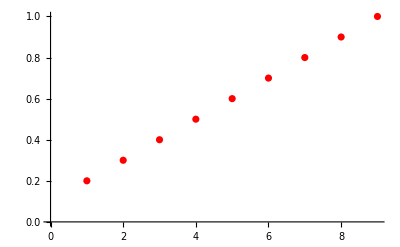

```mathematica
ListPlot[Transpose[Transpose[simutable][[1]]][[2]],PlotStyle->{Red,Thick}]
```

```mathematica
widthtable=Table[{{"d=",d/10},widthinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,1,10}]
```

{{{d=,1/10},{0.214368,0.123778,0.245901,0.782,0.22888}},{{d=,1/5},{0.226475,0.136282,0.264688,0.782,0.246616}},{{d=,3/10},{0.278099,0.159278,0.306629,0.874,0.285883}},{{d=,2/5},{0.335095,0.18835,0.358912,0.966,0.333146}},{{d=,1/2},{0.445933,0.219425,0.416515,1.058,0.386906}},{{d=,3/5},{0.502553,0.254718,0.484619,1.15,0.446443}},{{d=,7/10},{0.64142,0.293127,0.55745,1.242,0.512484}},{{d=,4/5},{0.716215,0.33302,0.63455,1.334,0.580942}},{{d=,9/10},{0.810045,0.37517,0.721498,1.426,0.651744}},{{d=,1},{0.896451,0.41511,0.795493,1.518,0.720805}}}

```mathematica
Transpose[Transpose[widthtable][[1]]][[2]]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[widthtable][[2]]][[1]]
```

{0.214368,0.226475,0.278099,0.335095,0.445933,0.502553,0.64142,0.716215,0.810045,0.896451}

```mathematica
Transpose[Transpose[widthtable][[2]]][[2]]
```

{0.123778,0.136282,0.159278,0.18835,0.219425,0.254718,0.293127,0.33302,0.37517,0.41511}

```mathematica
Transpose[Transpose[widthtable][[2]]][[3]]
```

{0.245901,0.264688,0.306629,0.358912,0.416515,0.484619,0.55745,0.63455,0.721498,0.795493}

```mathematica
Transpose[Transpose[widthtable][[2]]][[4]]
```

{0.782,0.782,0.874,0.966,1.058,1.15,1.242,1.334,1.426,1.518}

```mathematica
Transpose[Transpose[widthtable][[2]]][[5]]
```

{0.22888,0.246616,0.285883,0.333146,0.386906,0.446443,0.512484,0.580942,0.651744,0.720805}

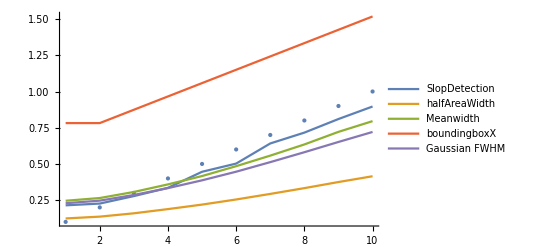

-Graphics-

```mathematica
Show[ListPlot[Transpose[Transpose[widthtable][[1]]][[2]],PlotStyle->{PointSize[Large]}],ListLinePlot[{Transpose[Transpose[widthtable][[2]]][[1]],Transpose[Transpose[widthtable][[2]]][[2]],Transpose[Transpose[widthtable][[2]]][[3]],Transpose[Transpose[widthtable][[2]]][[4]],Transpose[Transpose[widthtable][[2]]][[5]]},PlotLegends->{"SlopDetection","halfAreaWidth","Meanwidth","boundingboxX","Gaussian FWHM"}],PlotRange->All]
```

```mathematica
(*

*)
```